```mathematica
ClearAll
```

ClearAll

```mathematica
Dim = 6;
```

```mathematica
ψTrial[s_] := Module[{v1,v2,r1,r2,r12,retval},
v1 = {s[[1]],s[[2]],s[[3]]};
v2 = {s[[4]],s[[5]],s[[6]]}; 
r1 = Norm[v1];
r2 =Norm[v2]; 
r12 = Norm[v1-v2];
retval = Exp[-α r1] Exp[-α r2] Exp[r12 / (2 (1 + β r12))];
Return[retval]
];
```

```mathematica
LocalEnergy[s_] := Module[{v1,v2,r1,r2,r12,rdr,retval},
v1 = {s[[1]],s[[2]],s[[3]]};
v2 = {s[[4]],s[[5]],s[[6]]}; 
r1 = Norm[v1];
r2 = Norm[v2];
r12 = Norm[v1-v2];
rdr = Dot[v1,v2];
retval = - 2 α^2 + (2 α - 4)(1/r1+1/r2)+1/r12(2 - (r12 + 4 (1+ β r12))/(2 (1 + β r12)^4)+ (1/r1+1/r2)(r1 r2 - rdr)  α/(1 + β r12)^2);
Return[retval]
];
```

```mathematica
F[s_] := Module[{v1,v2,r1,r2,r12,rdr,retval},
v1 = {s[[1]],s[[2]],s[[3]]};
v2 = {s[[4]],s[[5]],s[[6]]}; 
r1 = Norm[v1];
r2 = Norm[v2];
r12 = Norm[v1-v2];
retval = - 2 α Join[1/r1 v1,1/r2 v2] + 1/(1 + β r12)^2 1/r12 Join[v1-v2,v2-v1];
Return[retval]
];
```

```mathematica
λ :=0.85/α;Step[s_] := s + λ Table[RandomReal[{-1,1}],{i,1,Dim}];
```

```mathematica
S0 := {0,0,1/α,0,0,-1/α};
```

```mathematica
α =1.8; β = 0.9;
```

```mathematica
InitializeWalkers[M_] := Module[
{z,ψψ,trialψψ,trialconfig,j,WalkerPositions,NTherm = 10000,count=1},
z =S0;
ψψ = Abs[ψTrial[z]]^2;
WalkerPositions=Table[0,{i,1,M}];
For[j = 0, j <= NTherm+10M, j++,
trialconfig = Step[z];
trialψψ = Abs[ψTrial[trialconfig]]^2;
If[trialψψ/ψψ≥ Random[Real,{0,1}],
z = trialconfig;
ψψ = trialψψ;
];
If[j > NTherm && Mod[j,10]==0,
WalkerPositions[[count]]=z;
count+= 1
];
];
Return[WalkerPositions]
]
```

```mathematica
ProposalProbability[rf_, ri_,dt_] := Exp[-1/(4*dt)(rf-ri-F[ri]dt).(rf-ri-F[ri]dt)];
WeighWalker[rf_,ri_,dt_] := Min[Floor[
Exp[ dt/2(2 E0 - LocalEnergy[ri]-LocalEnergy[rf])]+RandomReal[{0,1}]
],3];
```

```mathematica
MCStep1[positions_,dt_] := Module[{i,r,rp,w,weights, newpositions},
weights = Table[0,Length[positions]];
newpositions = Table[0,Length[positions]];
For[
i = 1, i ≤ Length[positions], i++,
r = positions[[i]];
rp = MoveWalker[r,dt];
(* I'm using the maximum number of 3 offspring suggested by Schulten et al. Doesn't seem to matter too much*)
w = Min[Floor[
Exp[ dt/2(2 E0 - LocalEnergy[r]-LocalEnergy[rp])]+RandomReal[{0,1}]
],3];
newpositions[[i]]= rp;
weights[[i]]= w
];
Return[RepackWalkers[weights,newpositions]];
]
```

```mathematica
MCStep2[positions_,dt_] := Module[{i,r,rp,w,weights, newpositions,eta,ψψ,trialψψ,prf,pri,pacc,bdist,b,wNoAcc},
weights = Table[0,Length[positions]];
newpositions = positions;
For[
i = 1, i ≤ Length[positions], i++,
r = positions[[i]];
rp = MoveWalker[r,dt];
pacc = Min[1, (ProposalProbability[r,rp,dt]*Abs[ψTrial[rp]]^2)/(ProposalProbability[rp,r,dt]*Abs[ψTrial[r]]^2)];
eta = RandomReal[{0,1}];
If[pacc> eta,
newpositions[[i]]= rp;
weights[[i]]= WeighWalker[rp,r,dt],
weights[[i]] = WeighWalker[r,r,dt];
];
];
Return[RepackWalkers[weights,newpositions]];
]
```

```mathematica
MoveWalker[r_, dt_] := r + Table[RandomReal[NormalDistribution[0.0,Sqrt[2dt]]],{i,1,Dim}] + dt F[r]
```

```mathematica
RepackWalkers[weights_,positions_] := Module[{retval},
retval = Partition[
Flatten[
Table[
Table[positions[[j]],{i,1,weights[[j]]}], {j,1,Length[weights]}]
],
Dim];
Return[retval]
]
```

```mathematica
Thermalize1[M_,Nsteps_,dt_,Z_,a_] := Module[{WalkerPositions,EList,j},
WalkerPositions = InitializeWalkers[M];
EList = Table[0,Nsteps];
(* Get the initial energy *)
E0 = Sum[LocalEnergy[WalkerPositions[[i]]],{i,1,Length[WalkerPositions]}]/Length[WalkerPositions];
(* If we're doing everything correctly, the initial E0 should be equal to the variational energy of our trial function.  I'll print it just so we can check that *)
Print["Initial energy is ",E0];
For[j = 1, j ≤ Nsteps, j++,
If[Mod[j,100]==0, Print[j]];
WalkerPositions= MCStep1[WalkerPositions,dt];
(* Every Z steps, update the energy to keep the number of walkers stable *)
If[Mod[j,Z]==0,
E0 = E0 + a/dt(1- Length[WalkerPositions]/M)
];
EList[[j]]=Total[Map[LocalEnergy,WalkerPositions]]/Length[WalkerPositions];
If[Length[WalkerPositions]==0, Print["All Walkers Dead!"];Return[{EList,WalkerPositions}]]
];
EList = Accumulate[EList]/Table[i,{i,1,Length[EList]}];
Return[{EList,WalkerPositions}]
]
```

```mathematica
Thermalize2[M_,Nsteps_,dt_,Z_,a_] := Module[{WalkerPositions,EList,j},
WalkerPositions = InitializeWalkers[M];
EList = Table[0,Nsteps+1];
(* Get the initial energy *)
E0 = Sum[LocalEnergy[WalkerPositions[[i]]],{i,1,Length[WalkerPositions]}]/Length[WalkerPositions];
(* If we're doing everything correctly, the initial E0 should be equal to the variational energy of our trial function.  I'll print it just so we can check that *)
Print["Initial energy is ",E0];
For[j = 1, j ≤ Nsteps, j++,
WalkerPositions= MCStep2[WalkerPositions,dt];
(* Every Z steps, update the energy to keep the number of walkers stable *)
If[Mod[j,Z]==0,
E0 = E0 + a/dt(1- Length[WalkerPositions]/M)
];
EList[[j]]=Total[Map[LocalEnergy,WalkerPositions]]/Length[WalkerPositions];
If[Length[WalkerPositions]==0, Print["All Walkers Dead!"];Return[{EList,WalkerPositions}]]
];
EList = Accumulate[EList]/Table[i,{i,1,Length[EList]}];
Return[{EList,WalkerPositions}]
]
```

```mathematica
GetBins[psi_] := Module[{},
Return[BinCounts[psi,{xmin,xmax,(xmax-xmin)/nb}]]
]
```

```mathematica
Measure2[M_,Nsteps_,dt_,Z_,a_,lastwalker_] := Module[{WalkerPositions,EList,j, wfn},
WalkerPositions = lastwalker;
EList = Table[0,Nsteps];
For[j = 1, j ≤ Nsteps, j++,
If[Mod[j,100]==0, Print[j]];
WalkerPositions= MCStep2[WalkerPositions,dt];
(* Every Z steps, update the energy to keep the number of walkers stable *)
If[Mod[j,Z]==0,
E0 = E0 + a/dt(1- Length[WalkerPositions]/M)
];
EList[[j]]=Total[Map[LocalEnergy,WalkerPositions]]/Length[WalkerPositions];
If[Length[WalkerPositions]==0, Print["All Walkers Dead!"];Return[{EList,WalkerPositions}]]
];
Return[EList]
]
```

```mathematica
Measure1[M_,Nsteps_,dt_,Z_,a_,lastwalker_] := Module[{WalkerPositions,EList,j, wfn},
WalkerPositions = lastwalker;
EList = Table[0,Nsteps];
For[j = 1, j ≤ Nsteps, j++,
If[Mod[j,100]==0, Print[j]];
WalkerPositions= MCStep1[WalkerPositions,dt];
(* Every Z steps, update the energy to keep the number of walkers stable *)
If[Mod[j,Z]==0,
E0 = E0 + a/dt(1- Length[WalkerPositions]/M)
];
EList[[j]]=Total[Map[LocalEnergy,WalkerPositions]]/Length[WalkerPositions];
If[Length[WalkerPositions]==0, Print["All Walkers Dead!"];Return[{EList,WalkerPositions}]]
];
Return[EList]
]
```

```mathematica
VQMCStats[data_,Nbins_]:=Module[
{bindata,binmeans,bin2means,value,uncertainty},
bindata = Partition[data,Length[data]/Nbins];
binmeans = Map[Mean,bindata];
bin2means = binmeans^2;
value = Mean[binmeans];
uncertainty =Sqrt[1/(Nbins-1)(1/Nbins Total[bin2means] - (1/Nbins Total[binmeans])^2)];
Return[{value,uncertainty}]
]
```

```mathematica
GetThermTime[etherm_] := Module[{},
For[i =1, i ≤ Length[etherm], i++,
If[etherm[[i]] ≤ (0.997*5.807),
Return[i];]]]
```

```mathematica
M = 4000; dt = 0.005; Z = 1; a =1;
data1 = Table[{0.,0.,0.,0.,0.,0.}, {i, 1, 10}];
data2 = Table[{0.,0.,0.,0.,0,,0.}, {i, 1, 10}];
energieslist1 = Table[{0.,0.},{i, 1, 10}];
energieslist2 = Table[{0.,0.},{i, 1, 10}];
data1[[1]][[5]]
energieslist1[[1,1]]
```

0.

0.

```mathematica
DoCalc[M_,dt_,Z_,a_]:= Module[{i,data1,data2,energieslist1,energieslist2,energiestherm1,lastwalker1,energiestherm2,lastwalker2,stats1,stats2,energies1,energies2},
data1 = Table[{0.,0.,0.,0.,0.,0.}, {i, 1, 10}];
data2 = Table[{0.,0.,0.,0.,0,0.}, {i, 1, 10}];
energieslist1 = Table[{0.,0.},{i, 1, 10}];
energieslist2 = Table[{0.,0.},{i, 1, 10}];
For[i = 1, i ≤ 10, i++,
Print["now on iteration ", i];
data1[[i]][[5]]= Timing[{energiestherm1,lastwalker1}=Thermalize1[M,500,dt,Z,a];][[1]];
energieslist1[[i,1]]=energiestherm1;
data1[[i]][[4]] = GetThermTime[energiestherm1];
data2[[i]][[5]] = Timing[{energiestherm2,lastwalker2}=Thermalize2[M,500,dt,Z,a];][[1]];
energieslist2[[i,1]]=energiestherm2;
data2[[i]][[4]] = GetThermTime[energiestherm2];
data1[[i]][[6]]= Timing[energies1=Measure1[M,1000,dt,Z,a,lastwalker1];][[1]];
energieslist1[[i,2]]=energies1;
data2[[i]][[6]] = Timing[energies2=Measure2[M,1000,dt,Z,a,lastwalker2];][[1]];
energieslist2[[i,2]]=energies2;
stats1 = VQMCStats[energies1,10];
data1[[i]][[1]] = stats1[[1]];
data1[[i]][[2]] = stats1[[2]];
data1[[i]][[3]] = (stats1[[1]]+5.807)/5.807;
stats2 = VQMCStats[energies2,10];
data2[[i]][[1]] = stats2[[1]];
data2[[i]][[2]] = stats2[[2]];
data2[[i]][[3]] = (stats2[[1]]+5.807)/5.807;
];
Return[{data1,data2,energieslist1,energieslist2}];
]
```

```mathematica
results = DoCalc[M,dt,Z,a];
```

now on iteration 1

Initial energy is -5.72693

100

200

300

400

500

Initial energy is -5.78498

100

200

300

400

500

600

700

800

900

1000

100

200

300

400

500

600

700

800

900

1000

now on iteration 2

Initial energy is -5.80113

100

200

300

400

500

Initial energy is -5.74079

100

200

300

400

500

600

700

800

900

1000

100

200

300

400

500

600

700

800

900

1000

now on iteration 3

Initial energy is -5.75731

100

200

300

400

500

Initial energy is -5.77155

100

200

300

400

500

600

700

800

900

1000

100

200

300

400

500

600

700

800

900

1000

now on iteration 4

Initial energy is -5.75691

100

200

300

400

500

Initial energy is -5.75932

100

200

300

400

500

600

700

800

900

1000

100

200

300

400

500

600

700

800

900

1000

now on iteration 5

Initial energy is -5.74409

100

200

300

400

500

Initial energy is -5.76884

100

200

300

400

500

600

700

800

900

1000

100

200

300

400

500

600

700

800

900

1000

now on iteration 6

Initial energy is -5.76011

100

200

300

400

500

Initial energy is -5.74092

100

200

300

400

500

600

700

800

900

1000

100

200

300

400

500

600

700

800

900

1000

now on iteration 7

Initial energy is -5.76403

100

200

300

400

500

Initial energy is -5.76788

100

200

300

400

500

600

700

800

900

1000

100

200

300

400

500

600

700

800

900

1000

now on iteration 8

Initial energy is -5.76705

100

200

300

400

500

Initial energy is -5.75559

100

200

300

400

500

600

700

800

900

1000

100

200

300

400

500

600

700

800

900

1000

now on iteration 9

Initial energy is -5.75813

100

200

300

400

500

Initial energy is -5.76188

100

200

300

400

500

600

700

800

900

1000

100

200

300

400

500

600

700

800

900

1000

now on iteration 10

Initial energy is -5.74517

100

200

300

400

500

Initial energy is -5.75128

100

200

300

400

500

600

700

800

900

1000

100

200

300

400

500

600

700

800

900

1000

```mathematica
resultsUse = results;
```

```mathematica
resultsUse[[1]]
```

{{-5.7825,0.00263517,0.00421954,1,515.918,911.179},{-5.79057,0.00223659,0.00282876,1,397.344,788.291},{-5.79076,0.00171004,0.00279746,1,411.938,816.12},{-5.79048,0.00213039,0.00284522,1,406.376,841.723},{-5.79415,0.00354139,0.00221294,1,394.566,865.894},{-5.78989,0.00316638,0.0029463,1,425.013,791.202},{-5.7851,0.00197859,0.00377176,1,423.743,892.694},{-5.79178,0.00155698,0.00262046,1,395.544,851.182},{-5.79177,0.00267356,0.00262245,1,454.678,920.855},{-5.78942,0.00139297,0.00302751,1,397.144,948.813}}

```mathematica
avgE={0.,0.};
For[i = 1, i ≤ 10, i++,
avgE = avgE + {resultsUse[[1,i,1]],resultsUse[[2,i,1]]};];
avgE = avgE /10;
avgE = {Labeled[avgE[[1]], "-5.790 Ry", Top], Labeled[avgE[[2]], "-5.810 Ry", Top]}
avgErr = {0.,0.};
For[i = 1, i ≤ 10, i++,
avgErr = avgErr + {Abs[resultsUse[[1,i,3]]],Abs[resultsUse[[2,i,3]]]};];
avgErr = 5.807*avgErr/10;
avgErr = {Labeled[avgErr[[1]], "0.017 Ry", Top], Labeled[avgErr[[2]], "0.003 Ry", Top]}
```

{-5.78964-5.790 Ry,-5.80986-5.810 Ry}

{0.01735850.017 Ry,0.003466820.003 Ry}

```mathematica
EwErr = {Around[avgE[[1]],avgErr[[1]]],Around[avgE[[2]],avgErr[[2]]]}
```

{-5.78964-5.790 Ry0.01735850.017 Ry,-5.80986-5.810 Ry0.003466820.003 Ry}

```mathematica
BarChart[avgE,ScalingFunctions->"Reverse",PlotRange->{-5.78,-5.82}, BarSpacing->Large,GridLines->{None,{{-5.807,Thick}}},ChartStyle->{Red, Green},PlotLabel->"Averge Energy",LabelStyle->{GrayLevel[0]},ChartLegends->{"Basic","Modified"},ChartLabels->{"Basic","Modified"},AxesLabel->"Energy (Ry)"]
```

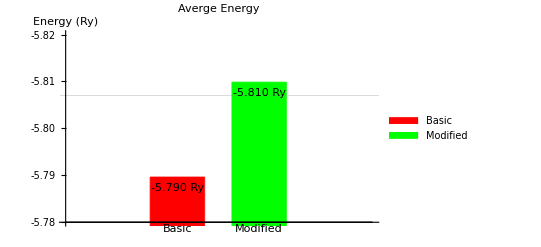

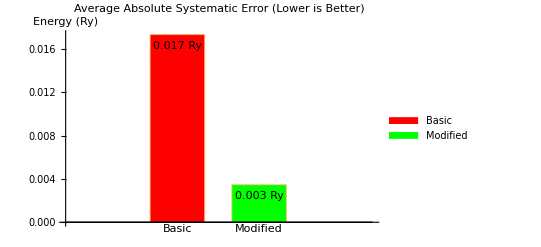

```mathematica
BarChart[avgErr,PlotRange->All, BarSpacing->Large,GridLines->None,ChartStyle->{Red, Green},PlotLabel->"Average Absolute Systematic Error (Lower is Better)",LabelStyle->{GrayLevel[0]},ChartLegends->{"Basic","Modified"},ChartLabels->{"Basic","Modified"},AxesLabel->"Energy (Ry)"]
```

```mathematica
avgStErr = {0.,0.};
For[i = 1, i ≤ 10, i++,
avgStErr = avgStErr + {resultsUse[[1,i,2]],resultsUse[[2,i,2]]};];
avgStErr = avgStErr/10;
avgStErr = {Labeled[avgStErr[[1]], "0.0023 Ry", Top], Labeled[avgStErr[[2]], "0.0025 Ry", Top]}
```

{0.002302210.0023 Ry,0.002537440.0025 Ry}

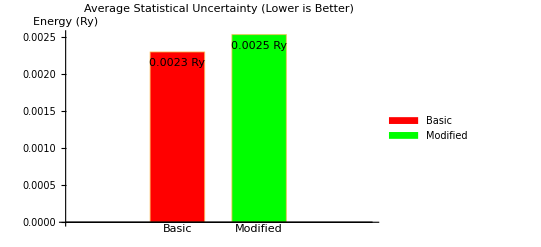

```mathematica
BarChart[avgStErr,PlotRange->All, BarSpacing->Large,GridLines->None,ChartStyle->{Red, Green},PlotLabel->"Average Statistical Uncertainty (Lower is Better)",LabelStyle->{GrayLevel[0]},ChartLegends->{"Basic","Modified"},ChartLabels->{"Basic","Modified"},AxesLabel->"Energy (Ry)"]
```

```mathematica
avgT = {0.,0.}
For[i = 1, i ≤ 10, i++,
avgT = avgT + {resultsUse[[1,i,5]]+resultsUse[[1,i,6]],resultsUse[[2,i,5]]+resultsUse[[2,i,6]]};];
avgT = avgT /600;
avgT = {Labeled[avgT[[1]], "21.4 mins", Top], Labeled[avgT[[2]], "48.2 mins", Top]}
```

{0.,0.}

{21.41721.4 mins,48.208248.2 mins}

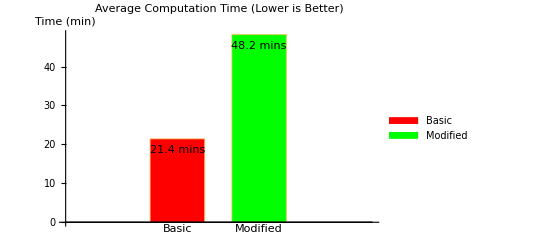

```mathematica
BarChart[avgT,PlotRange->All, BarSpacing->Large,GridLines->None,ChartStyle->{Red, Green},PlotLabel->"Average Computation Time (Lower is Better)",LabelStyle->{GrayLevel[0]},ChartLegends->{"Basic","Modified"},ChartLabels->{"Basic","Modified"},AxesLabel->"Time (min)"]
```

```mathematica
Map[Mean,{{1,2},{2,3},{3,4},{4,5}}]
```

```mathematica
\text{SwatchLegend}\left[\left\{\text{Directive}\left[\text{EdgeForm}[\text{Directive}[\text{Thickness}[\text{Small}],\text{Opacity}[0.686]]],\fbox{$$}\right],\text{Directive}\left[\text{EdgeForm}[\text{Directive}[\text{Thickness}[\text{Small}],\text{Opacity}[0.686]]],\fbox{$$}\right]\right\},\{\text{Basic},\text{Modified}\},\text{LegendMarkers}\to\left(
\begin{array}{cc}\text{Automatic}&\text{Automatic} \\\end{array} \right),\text{LabelStyle}\to\left(
\begin{array}{c}\fbox{$$} \\\fbox{$$} \\\end{array} \right),\text{LegendLayout}\to\text{Column}\right]
```

{3/2,5/2,7/2,9/2}

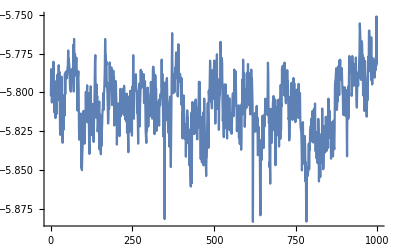

```mathematica
ListPlot[resultsUse[[4,3,2]], Joined-> True, PlotRange-> All]
```

```mathematica
Timing[energies=Measure2[M,1000,dt,Z,a,lastwalker];]
```

100

200

300

400

500

600

700

800

900

1000

{1651.74,Null}

```mathematica
VQMCStats[energies,10]
```

{-5.8007,0.00270503}

```mathematica
(VQMCStats[energies,10][[1]]+5.807)/5.807
```

0.0010853